# Mosaic Chart

#### rectanglesForMosaicChart

```mathematica
ClearAll[rectanglesForMosaicChart];
rectanglesForMosaicChart[data_List,observation1_Integer,observation2_Integer,nTimes_Integer,widthPadding_Integer,heightPadding_Integer,pt_Integer,offsetX_Integer,offsetY_Integer]:=Block[{
keys1,keys2,dataCounts,observation1Data,observation2Data,countsObs1,countsObs2,rectanglesWithMetaData,hStart,wStart,maxWidth,rectangleToAppend,toottipText,xCoordinateOfBox,yCoordinateOfBox,arrayOfColor,colorPanel,textXArray,textYArray
},
keys2=Sort@Keys[Counts[data[[;;,observation2]]]];
keys1=Sort@Keys[Counts[data[[;;,observation1]]]];
countsObs1=Plus@@CountsBy[data,#[[observation1]]&];
countsObs2=Plus@@CountsBy[data,#[[observation2]]&];
observation1Data=CountsBy[data,#[[observation1]]&];
observation2Data=CountsBy[data,#[[observation2]]&];
dataCounts=KeySort@CountsBy[data,{#[[observation1]],#[[observation2]]}&];
(**Print[keys1, keys2, observation1Data,observation2Data, "\n 1:",countsObs1,"; 2:",countsObs2,"\n",dataCounts];**)
(**Print["===\n", keys1,observation1Data,countsObs1];**)
arrayOfColor=Reverse[ColorData["Rainbow"][#]&/@Range[0,1,1/(Length[keys1]-1)]];
colorPanel=Table[Blend[{arrayOfColor⟦i⟧,LightGray},#/Length[keys2]]&/@Range[0,Length[keys2]-1],{i,1,Length[arrayOfColor]}];
textYArray={};
hStart=0;
For[j=1,j<=Length[keys2],j++,
yCoordinateOfBox=hStart+dataCounts[{keys1[[1]],keys2[[j]]}]/observation1Data[keys1[[1]]]*nTimes;
yCoordinateOfBox=yCoordinateOfBox/.{_Missing->0};
textYArray=Append[textYArray,Text[Style[keys2[[j]],pt],{-((pt-1)/2)+offsetY,hStart+(yCoordinateOfBox-hStart)/2}]];
hStart=yCoordinateOfBox+heightPadding;
];
wStart=0;
rectanglesWithMetaData={};
textXArray={};
For[i = 1,i<=Length[keys1],i++,
hStart=0;
maxWidth=0;
For[j=1,j<=Length[keys2],j++,
rectanglesWithMetaData=Append[rectanglesWithMetaData,colorPanel⟦i,j⟧];
xCoordinateOfBox=wStart+observation1Data[keys1[[i]]]/countsObs1*nTimes;
yCoordinateOfBox=hStart+dataCounts[{keys1[[i]],keys2[[j]]}]/observation1Data[keys1[[i]]]*nTimes;
xCoordinateOfBox=xCoordinateOfBox/.{_Missing->0};
yCoordinateOfBox=yCoordinateOfBox/.{_Missing->0};

rectangleToAppend=Rectangle[{wStart,hStart},{xCoordinateOfBox,yCoordinateOfBox}];

toottipText={keys1[[i]],keys2[[j]],dataCounts[{keys1[[i]],keys2[[j]]}]/.{_Missing->0}};

rectangleToAppend=Tooltip[rectangleToAppend,toottipText];

hStart=yCoordinateOfBox+heightPadding;

rectanglesWithMetaData=Append[rectanglesWithMetaData,rectangleToAppend];
];
textXArray=Append[textXArray,Text[Style[keys1[[i]],pt],{(xCoordinateOfBox-wStart)/2+wStart,-((pt-1)/2)+offsetX}]];
wStart=xCoordinateOfBox+widthPadding;
];
{rectanglesWithMetaData,textXArray,textYArray}
];
```

#### MosaicChart

```mathematica
ClearAll[MosaicChart];
MosaicChart[{data_List,observation1_Integer,observation2_Integer},OptionsPattern[{nTimes->100,widthPadding->10,heightPadding->10,pt->11,offsetX->0,offsetY->0}]]:=
Graphics[rectanglesForMosaicChart[data,observation1,observation2,OptionValue[nTimes],OptionValue[widthPadding],OptionValue[heightPadding],OptionValue[pt],OptionValue[offsetX],OptionValue[offsetY]]];
```

# Test

```mathematica
myData1=Table[{RandomChoice[{"м","ж"}],RandomChoice[{"да","нет"}]},{i,1,100}];
myData2=Table[{RandomChoice[{"м","ж"}],RandomChoice[Range[4,12]]},{i,1,100}];
```

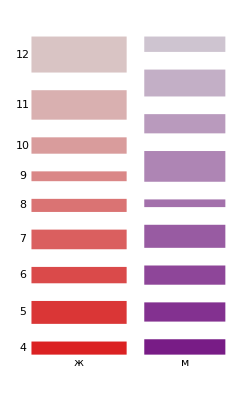

```mathematica
MosaicChart[{myData2,1,2}]
```